# Vaje iz Mathematice, 2. del

### 1. naloga:

Izračunaj vrednost izraza  30! -20! +110

```mathematica
t1a = 30! -20! + 110
```

265252859812188625734300303360110

Kakšna je 10. števka od leve proti desni?

```mathematica
Mod[Quotient[t1a,10^10],10]
```

0

Rezultat razcepi na prafaktorje.

```mathematica
t1b = FactorInteger[t1a];
t1c =Table[t1b[[i]][[1]],{i,Length[t1b]}]
```

{2,5,11,41,101,897840721,5360156751159421}

Katero je največje praštevilo v razcepu?

```mathematica
Last[t1c]
```

5360156751159421

Katero praštevilo nastopa v razcepu z najvišjo potenco?

```mathematica
First[Last[SortBy[t1b,Last]]]
```

11

### 2. naloga:

Poišči vse delitelje števila 16524000.

```mathematica
t2a = Divisors[16524000]
```

{1,2,3,4,5,6,8,9,10,12,15,16,17,18,20,24,25,27,30,32,34,36,40,45,48,50,51,54,60,68,72,75,80,81,85,90,96,100,102,108,120,125,135,136,144,150,153,160,162,170,180,200,204,216,225,240,243,250,255,270,272,288,300,306,324,340,360,375,400,405,408,425,432,450,459,480,486,500,510,540,544,600,612,648,675,680,720,750,765,800,810,816,850,864,900,918,972,1000,1020,1080,1125,1200,1215,1224,1275,1296,1350,1360,1377,1440,1500,1530,1620,1632,1700,1800,1836,1944,2000,2025,2040,2125,2160,2250,2295,2400,2430,2448,2550,2592,2700,2720,2754,3000,3060,3240,3375,3400,3600,3672,3825,3888,4000,4050,4080,4131,4250,4320,4500,4590,4860,4896,5100,5400,5508,6000,6075,6120,6375,6480,6750,6800,6885,7200,7344,7650,7776,8100,8160,8262,8500,9000,9180,9720,10125,10200,10800,11016,11475,12000,12150,12240,12750,12960,13500,13600,13770,14688,15300,16200,16524,17000,18000,18360,19125,19440,20250,20400,20655,21600,22032,22950,24300,24480,25500,27000,27540,30375,30600,32400,33048,34000,34425,36000,36720,38250,38880,40500,40800,41310,44064,45900,48600,51000,54000,55080,57375,60750,61200,64800,66096,68000,68850,73440,76500,81000,82620,91800,97200,102000,103275,108000,110160,114750,121500,122400,132192,137700,153000,162000,165240,172125,183600,194400,204000,206550,220320,229500,243000,275400,306000,324000,330480,344250,367200,413100,459000,486000,516375,550800,612000,660960,688500,826200,918000,972000,1032750,1101600,1377000,1652400,1836000,2065500,2754000,3304800,4131000,5508000,8262000,16524000}

Katera od njih so praštevila?

```mathematica
Select[t2a,PrimeQ]
```

{2,3,5,17}

S kakšnimi potencami nastopajo v razcepu števila 16524000?

```mathematica
FactorInteger[16524000]
```

{{2,5},{3,5},{5,3},{17,1}}

### 3. naloga:

Izračunaj  lim_(x→2) (x^3-4 x^2+2x+4)/(x^5-9x-14)

```mathematica
Limit[(x^3-4 x^2+2x+4)/(x^5-9x-14),x->2]
```

-2/71

Izračunaj  lim_(x→0) (arctg (7x))/(arcsin (8x))

```mathematica
Limit[ArcTan[7x]/ArcSin[8x],x->0]
```

7/8

Izračunaj  lim_(x→5) (x^2-25)ctg (π x)

```mathematica
Limit[(x^2-25)Cot [Pi x],x->5]
```

10/π

Izračunaj  lim_(x→π) (1+cos x)/(2 √(π x)-π-x)

```mathematica
Limit[(1+Cos[x])/(2 √(Pi x)-Pi-x),x->Pi]
```

-2 π

Izračunaj levo limito:  lim_(x→0^-) |x|ctg x

```mathematica
Limit[Abs[x]Cot[x],x->0,Direction->"FromBelow"]
```

-1

Izračunaj desno limito:  lim_(x→0^+) |x|ctg x

```mathematica
Limit[Abs[x]Cot[x],x->0,Direction->"FromAbove"]
```

1

### 4. naloga:

Izračunaj prvi odvod funkcije  y=2sin (2x+1)  cos (x)

```mathematica
t4a[x_] = 2Sin[2x+1]Cos[x];
t4a'[x]
```

4 Cos[x] Cos[1+2 x]-2 Sin[x] Sin[1+2 x]

Izračunaj prvi odvod funkcije  y=x ln (2x)

```mathematica
t4b[x_] = x Log[2x];
t4b'[x]
```

1+Log[2 x]

Izračunaj prvi odvod funkcije  y=(3x-2)^(1/3)/(√(2x+1))

```mathematica
t4c[x_] = (3x-2)^(1/3)/(√(2x+1));
t4c'[x]
```

1/(√(1+2 x) (-2+3 x)^(2/3))-(-2+3 x)^(1/3)/(1+2 x)^(3/2)

Izračunaj drugi odvod funkcije  y=(x+1)^x

```mathematica
t4d[x_] = (x+1)^x;
t4d''[x]
```

(1+x)^x (-x/(1+x)^2+2/(1+x))+(1+x)^x (x/(1+x)+Log[1+x])^2

### 5. naloga:

Numerično izračunaj ničle polinoma  x^7-2 x^6-x^5-2 x^4+12 x^2-x+1.

```mathematica
t5a=NSolve[x^7-2 x^6-x^5-2 x^4+12 x^2-x+1==0];
x/.t5a
```

{-1.37527,-0.356206-1.47367 ⅈ,-0.356206+1.47367 ⅈ,0.040941-0.283889 ⅈ,0.040941+0.283889 ⅈ,1.59494,2.41086}

Katere od teh ničel so realne?

```mathematica
Select[x/.t5a,Element[#,Reals]&]
```

{-1.37527,1.59494,2.41086}

Kakšna je največja absolutna vrednost ničle?

```mathematica
Max[Abs[x]/.t5a]
```

2.41086

### 6. naloga:

Razcepi polinom  x^7+2 x^6-80 x^5+232 x^4+175 x^3-826 x^2+256x-1056  na linearne in kvadratne faktorje.

```mathematica
Factor[x^7+2 x^6-80 x^5+232 x^4+175 x^3-826 x^2+256x-1056]
```

(-4+x)^2 (-3+x) (2+x) (11+x) (1+x^2)

Razcepi isti polinom na linearne faktorje.

```mathematica
Factor[x^7+2 x^6-80 x^5+232 x^4+175 x^3-826 x^2+256x-1056,Extension->I]
```

(-4+x)^2 (-3+x) (-ⅈ+x) (ⅈ+x) (2+x) (11+x)

Faktoriziraj trigonometrični izraz  sin (x)+cos (2x)

```mathematica
Factor[Sin[x]+Cos[2x], Trig->True] //Simplify
```

1+Sin[x]-2 Sin[x]^2

### 7. naloga:

Definiraj polinom  (x^2 (y-1)-x^3 y^5+(x-1)^7 x y (x^2+2x y+y^3))^2  kot novo spremenljivko.

```mathematica
t7a =(x^2 (y-1)-x^3 y^5+(x-1)^7 x y (x^2+2x y+y^3))^2
```

(x^2 (-1+y)-x^3 y^5+(-1+x)^7 x y (x^2+2 x y+y^3))^2

Razširi polinom tako, da dobiš vsoto monomov.

```mathematica
Expand[t7a]
```

x^4-2 x^4 y+2 x^5 y-14 x^6 y+42 x^7 y-70 x^8 y+70 x^9 y-42 x^10 y+14 x^11 y-2 x^12 y+5 x^4 y^2-30 x^5 y^2+99 x^6 y^2-196 x^7 y^2+301 x^8 y^2-518 x^9 y^2+1071 x^10 y^2-2020 x^11 y^2+3005 x^12 y^2-3432 x^13 y^2+3003 x^14 y^2-2002 x^15 y^2+1001 x^16 y^2-364 x^17 y^2+91 x^18 y^2-14 x^19 y^2+x^20 y^2-4 x^4 y^3+32 x^5 y^3-140 x^6 y^3+504 x^7 y^3-1596 x^8 y^3+4088 x^9 y^3-8036 x^10 y^3+12016 x^11 y^3-13728 x^12 y^3+12012 x^13 y^3-8008 x^14 y^3+4004 x^15 y^3-1456 x^16 y^3+364 x^17 y^3-56 x^18 y^3+4 x^19 y^3+2 x^3 y^4-10 x^4 y^4-14 x^5 y^4+294 x^6 y^4-1386 x^7 y^4+3962 x^8 y^4-7994 x^9 y^4+12010 x^10 y^4-13728 x^11 y^4+12012 x^12 y^4-8008 x^13 y^4+4004 x^14 y^4-1456 x^15 y^4+364 x^16 y^4-56 x^17 y^4+4 x^18 y^4-2 x^3 y^5+16 x^4 y^5-68 x^5 y^5+252 x^6 y^5-798 x^7 y^5+2044 x^8 y^5-4018 x^9 y^5+6008 x^10 y^5-6864 x^11 y^5+6006 x^12 y^5-4004 x^13 y^5+2002 x^14 y^5-728 x^15 y^5+182 x^16 y^5-28 x^17 y^5+2 x^18 y^5+4 x^3 y^6-56 x^4 y^6+362 x^5 y^6-1454 x^6 y^6+3990 x^7 y^6-7966 x^8 y^6+11942 x^9 y^6-13658 x^10 y^6+11970 x^11 y^6-7994 x^12 y^6+4002 x^13 y^6-1456 x^14 y^6+364 x^15 y^6-56 x^16 y^6+4 x^17 y^6+4 x^5 y^7-28 x^6 y^7+84 x^7 y^7-140 x^8 y^7+140 x^9 y^7-84 x^10 y^7+28 x^11 y^7-4 x^12 y^7+x^2 y^8-14 x^3 y^8+91 x^4 y^8-364 x^5 y^8+1001 x^6 y^8-2002 x^7 y^8+3003 x^8 y^8-3432 x^9 y^8+3003 x^10 y^8-2002 x^11 y^8+1001 x^12 y^8-364 x^13 y^8+91 x^14 y^8-14 x^15 y^8+x^16 y^8+2 x^4 y^9-14 x^5 y^9+42 x^6 y^9-70 x^7 y^9+70 x^8 y^9-42 x^9 y^9+14 x^10 y^9-2 x^11 y^9+x^6 y^10

Razvij polinom po potencah x  (koeficienti bodo polinomi v y).

```mathematica
Collect[t7a,x]
```

x^20 y^2+x^2 y^8+x^19 (-14 y^2+4 y^3)+x^18 (91 y^2-56 y^3+4 y^4+2 y^5)+x^17 (-364 y^2+364 y^3-56 y^4-28 y^5+4 y^6)+x^13 (-3432 y^2+12012 y^3-8008 y^4-4004 y^5+4002 y^6-364 y^8)+x^3 (-2 (-1+y) y^4+4 y^6-14 y^8)+x^15 (-2002 y^2+4004 y^3-1456 y^4-728 y^5+364 y^6-14 y^8)+x^16 (1001 y^2-1456 y^3+364 y^4+182 y^5-56 y^6+y^8)+x^14 (3003 y^2-8008 y^3+4004 y^4+2002 y^5-1456 y^6+91 y^8)+x^12 (2 (-1+y) y+3003 y^2-13728 y^3+12012 y^4+6006 y^5-7994 y^6-4 y^7+1001 y^8)+x^7 (-42 (-1+y) y-14 y^2+140 (-1+y) y^2+364 y^3-1456 y^4-70 (-1+y) y^4-728 y^5+3990 y^6+84 y^7-2002 y^8-70 y^9)+x^9 (-70 (-1+y) y-364 y^2+84 (-1+y) y^2+4004 y^3-8008 y^4-14 (-1+y) y^4-4004 y^5+11942 y^6+140 y^7-3432 y^8-42 y^9)+x^5 (-2 (-1+y) y+28 (-1+y) y^2+4 y^3-56 y^4-42 (-1+y) y^4-28 y^5-2 (-1+y) y^5+364 y^6+4 y^7-364 y^8-14 y^9)+x^11 (-14 (-1+y) y-2002 y^2+4 (-1+y) y^2+12012 y^3-13728 y^4-6864 y^5+11970 y^6+28 y^7-2002 y^8-2 y^9)+x^4 ((-1+y)^2-4 (-1+y) y^2+4 y^4+14 (-1+y) y^4+2 y^5-56 y^6+91 y^8+2 y^9)+x^10 (42 (-1+y) y+1001 y^2-28 (-1+y) y^2-8008 y^3+12012 y^4+2 (-1+y) y^4+6006 y^5-13658 y^6-84 y^7+3003 y^8+14 y^9)+x^8 (70 (-1+y) y+91 y^2-140 (-1+y) y^2-1456 y^3+4004 y^4+42 (-1+y) y^4+2002 y^5-7966 y^6-140 y^7+3003 y^8+70 y^9)+x^6 (14 (-1+y) y+y^2-84 (-1+y) y^2-56 y^3+364 y^4+70 (-1+y) y^4+182 y^5-1454 y^6-28 y^7+1001 y^8+42 y^9+y^10)

Kakšna je najvišja potenca posameznih spremenljivk, ki se pojavita v polinomu?

```mathematica
Exponent[t7a,{x,y}]
```

{20,10}

### 8.naloga:

Določi vsa realna števila, ki zadoščajo neenačbi  (|x-3|)/(x+1)>√(3-2x)

```mathematica
Reduce[Abs[x-3]/(x+1)>√(3-2x),x,Reals]
```

-1<x<1||1<x≤3/2

### 9. naloga:

Definiraj  (x^2-1)/(x^2-4)  kot funkcijo f spremenljivke x in nariši njen graf na intervalu [-5,5].

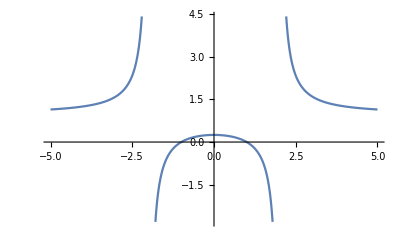

```mathematica
t9a[x_] = (x^2-1)/(x^2-4);
Plot[t9a[x],{x,-5,5}]
```

Določi ničle.

```mathematica
x/.Solve[t9a[x]==0,x]
```

{-1,1}

Določi pole in razišči obnašanje funkcije v okolici polov.

```mathematica
Reduce[Not[FunctionDomain[t9a[x],x]]]
```

x==-2||x==2

Izračunaj limiti v neskončnosti.

```mathematica
Limit[t9a[x],x->Infinity]
Limit[t9a[x],x->-Infinity]
```

1

1

Določi stacionarne točke.

```mathematica
t9b = Solve[t9a'[x]==0,x, Reals];
x/.t9b
```

{0}

Določi vrsto stacionarnih točk (lokalni minimum, lokalni maksimum, prevoj).

```mathematica
t9a''[x]/.t9b
```

{-3/8}

Določi intervale konveksnosti.

```mathematica
Reduce[t9a''[x]>0,x,Reals]
```

x<-2||x>2

Določi intervale konkavnosti.

```mathematica
Reduce[t9a''[x]<0,x,Reals]
```

-2<x<2

### 10. naloga:

Analiziraj funkcijo y=arctg x^2/(x^2-1). Zgleduj se po prejšnji nalogi.

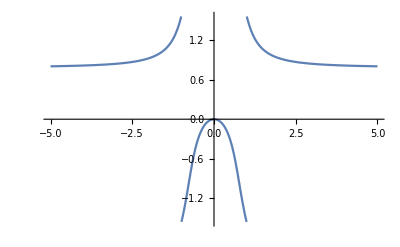

```mathematica
t10a[x_]= ArcTan[x^2/(x^2-1)];
Quiet[Plot[t10a[x],{x,-5,5}]]
```

```mathematica
x/.Solve[t10a[x]==0,x]
```

{0}

```mathematica
Reduce[Not[FunctionDomain[t10a[x],x]]]
```

x==-1||x==1

```mathematica
Limit[t10a[x],x->Infinity]
Limit[t10a[x],x->-Infinity]
```

π/4

π/4

```mathematica
t10b = Solve[t10a'[x]==0,x,Reals];
x/.t10b
```

{0}

```mathematica
t10a''[x]/.t10b
```

{-2}

```mathematica
Reduce[t10a''[x]>0,x,Reals]
```

x<-√(1/6 (1+√7))||x>√(1/6 (1+√7))

```mathematica
Reduce[t10a''[x]<0,x,Reals]
```

-√(1/6 (1+√7))<x<√(1/6 (1+√7))

### 11. naloga:

Določi tangento na funkcijo h(x)=sin^2 x-cos x  v točki x=2. Rezultat predstavi s sliko.

```mathematica
t11a[x_] =Sin[x]^2-Cos[x]
t11b =t11a'[2] //Simplify
```

-Cos[x]+Sin[x]^2

(1+2 Cos[2]) Sin[2]

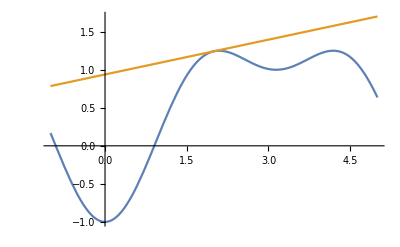

```mathematica
t11c =Solve[t11b*2+n==t11a[2],n,Reals];
Plot[{t11a[x],t11b*x+n/.t11c},{x,-1,5}]
```

### 12. naloga:

Dana sta vektorja  (v⃗)_1=(1,2,3)  in  (v⃗)_2=(-3,-2,5). Zapiši ju kot dve spremenljivki.

```mathematica
t12a= {1,2,3}
t12b = {-3,-2,5}
```

{1,2,3}

{-3,-2,5}

Izračunaj njun skalarni produkt.

```mathematica
t12a.t12b
```

8

Izračunaj njun vektorski produkt.

```mathematica
t12a×t12b
```

{16,-14,4}

Kateri od vektorjev je daljši?

```mathematica
Norm[t12b]>Norm[t12a]
```

True

Sestavi enačbo ravnine, ki gre skozi točko (1,1,1) in ima normalo v smeri vektorskega produkta.

```mathematica
a*x+b*y+c*z==d/.Solve[a+b+c==d&&{a,b,c}==(t12a×t12b)]
```

{16 x-14 y+4 z==6}

### 13. naloga:

Dana je matrika  M=(9 | 2 | -3
3 | 2 | 1
6 | 4 | -1).  Zapiši jo kot spremenljivko.

```mathematica
t13a = {
{9,2,-3},
{3,2,1},
{6,4,-1}
};
t13a //MatrixForm
```

(9 | 2 | -3
3 | 2 | 1
6 | 4 | -1)

Izračunaj njeno determinanto.

```mathematica
Det[t13a]
```

-36

Izračunaj njene lastne vrednosti.

```mathematica
Eigenvalues[t13a]
```

{3 (1+√2),4,3 (1-√2)}

Izračunaj njene lastne vektorje.

```mathematica
Eigenvectors[t13a]
```

{{-(-6-5 √2)/(6 (1+√2)),-(-2-√2)/(2 (1+√2)),1},{2,7,8},{-(-5+3 √2)/(3 √2 (-1+√2)),-(2-√2)/(2 (-1+√2)),1}}

Ali je matrika diagonalizabilna?

```mathematica
DiagonalizableMatrixQ[t13a]
```

True

Matriko želimo diagonalizirati. Konstruiraj diagonalno matriko (po diagonali ima lastne vrednosti), prehodno matriko (za stolpce ima lastne vektorje) in inverz prehodne matrike.

```mathematica
t13b =DiagonalMatrix[Eigenvalues[t13a]] ;
t13c = Transpose[Eigenvectors[t13a]];
t13d = Inverse[t13c];
t13b //MatrixForm
t13c //MatrixForm
t13d //MatrixForm
```

(3 (1+√2) | 0 | 0
0 | 4 | 0
0 | 0 | 3 (1-√2))

(-(-6-5 √2)/(6 (1+√2)) | 2 | -(-5+3 √2)/(3 √2 (-1+√2))
-(-2-√2)/(2 (1+√2)) | 7 | -(2-√2)/(2 (-1+√2))
1 | 8 | 1)

((7+8/(-1+√2)-(4 √2)/(-1+√2))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))) | (-2-8/(-1+√2)+(20 √2)/(3 (-1+√2)))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))) | (5/(-1+√2)-29/(3 √2 (-1+√2)))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2)))
(-1/(-1+√2)+1/(√2 (-1+√2))-1/(1+√2)-1/(√2 (1+√2)))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))) | (1/(-1+√2)-5/(3 √2 (-1+√2))+1/(1+√2)+5/(3 √2 (1+√2)))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))) | (2 √2)/(3 (-1+√2) (1+√2) (5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))))
(-7+8/(1+√2)+(4 √2)/(1+√2))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))) | (2-8/(1+√2)-(20 √2)/(3 (1+√2)))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))) | (5/(1+√2)+29/(3 √2 (1+√2)))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))))

Preveri, ali velja pogoj za diagonalizabilnost.

```mathematica
t13d.t13a.t13c ==t13b //Simplify
```

True

### 14. naloga:

Dana je parametrično podana krivulja  (((3-t) sin t)/(t+1),cos (t) sin (2t)). Definiraj jo kot funkcijo ene spremenljivke.

```mathematica
t14a[t_]={((3-t) Sin[t])/(t+1),Cos[t] Sin[2 t]}
```

{((3-t) Sin[t])/(1+t),Cos[t] Sin[2 t]}

Nariši krivuljo za  t∈[0,5].

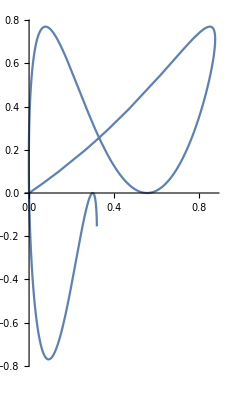

```mathematica
ParametricPlot[t14a[t],{t,0,5}]
```

Krivulja seče samo sebe natanko dvakrat. S pomočjo numeričnega reševanja enačb (FindRoot) poišči približek presečišč. Enačbo nastavi tako da izenačiš krivuljo, parametrizirano s parametrom t, s krivuljo, parametrizirano s parametrom s. Potem s spreminjanjem začetnih približkov parametrov t in s poskusi določiti vrednosti parametrov, pri katerih pride do samopresečič.

```mathematica
t14b={
FindRoot[t14a[t]==t14a[s],{{t,0.1},{s,2}}],
FindRoot[t14a[t]==t14a[s],{{t,0},{s,3}}]
}
```

{{t→0.130416,s→1.95093},{t→-2.79032×10^-20,s→3.14159}}

Iz dobljenih rešitev sestavi točki.

```mathematica
t14c = Point[t14a[t]]/.t14b
```

{Point[{0.330126,0.255695}],Point[{-8.37095×10^-20,-5.58064×10^-20}]}

Grafično preveri, ali gre za pravilen izračun.

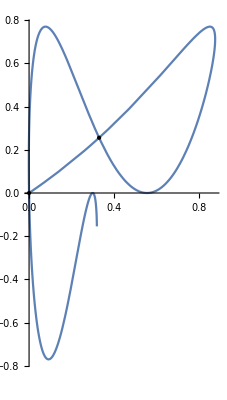

```mathematica
t14d =ParametricPlot[t14a[t],{t,0,5},Epilog->{PointSize->Large,t14c}]
```

### 15. naloga:

Naj bodo a⃗, b⃗ in c⃗ vektorji v R^3.
S simboličnim računom dokaži identiteto  a⃗×(b⃗×c⃗)=(a⃗·c⃗)b⃗-(a⃗·b⃗)c⃗

```mathematica
t15a = {a,b,c};
t15b = {i,j,k};
t15c={x,y,z};
t15a×(t15b×t15c) == (t15a.t15c)t15b -(t15a.t15b)t15c//Simplify
```

True

### 16. naloga:

Dokaži, da za poljubni 2×2 matriki A in B velja enakost  (A B)^-1=B^-1 A^-1.

```mathematica
t16a = {
{a,b},
{c,d}
};
t16b = {
{w,x},
{y,z}
};
Inverse[t16a.t16b] == Inverse[t16b].Inverse[t16a] // FullSimplify
```

True